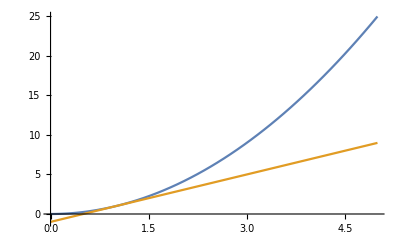

```mathematica
Plot[{x^2,2(x-1)+1,(q[t]^2-1)(x-1)/(q[t]-1)+1},{x,0,5},ImageSize->Full]
```

```mathematica
(*Ignore this stuff*) q[t_]=q[t_]=4(1-t)+a;
f[x_]=x^2;
a=1;
Manipulate[Show[{Plot[{f[x],(f[q[t]]-a)(x-a)/(q[t]-1)+f[a]},{x,0,5}],ListPlot[{{a,f[a]},{q[t],f[q[t]]}},PlotStyle->PointSize[.013]] },{PlotRange-> {-5,25},ImageSize->Full}],{t,0,.999999}]
```

```mathematica
(*Ignore this stuff, seriously*) q[t_]=4(1-t)+a;
f[x_]=x^2;
a=1;
Manipulate[Show[{Plot[{f[x],f'[a](x-a)+f[a],(f[q[t]]-a)(x-a)/(q[t]-1)+f[a]},{x,0,5}],ListPlot[{{a,f[a]},{q[t],f[q[t]]}},PlotStyle->PointSize[.013]] },{PlotRange-> {-5,25},ImageSize->Full}],{t,0,.999999}]
```